```mathematica
Mixing
```

## DEFINE PARAMTERS

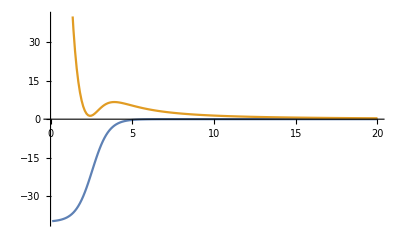

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=75;R=2.55;a=0.5;μ=8/9 Subscript[m, N];
E2=3;
rmax=20.;dr=0.1;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_,l_]:=(l(l+1)ℏc^2)/(2μ r^2);
V00[r_]:=Vwoods[r]+Vcent[r,0];
V22[r_]:=Vwoods[r]+Vcent[r,2];
V00mat=DiagonalMatrix[V00[rlist]];
V22mat=DiagonalMatrix[V22[rlist]];
(*MIXING*)
V02mat=V20mat=DiagonalMatrix[Vwoods[rlist]];
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H000:=V00mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
H022:=V22mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])+E2;
H0:=ArrayFlatten[{{H000,V02mat},{V20mat,H022}}];
ListLinePlot[{V00[rlist],V22[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

## BOUND SOLUTIONS

```mathematica
(*BOUND SOLUTION*)
κ0[En_]:=Sqrt[(2μ Abs[En])/ℏc^2];
κ2[En_]:=Sqrt[(2μ Abs[En+E2])/ℏc^2];
wavebound0[En_,r_]:=SphericalHankelH1[0,I κ0[En] r];
wavebound2[En_,r_]:=SphericalHankelH1[2,I κ2[En] r];
Bbound0[En_]:=rmax/wavebound0[En,rmax](D[wavebound0[En,r],r]/.r->rmax);
Bbound2[En_]:=rmax/wavebound2[En,rmax](D[wavebound2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewbound[En_]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound2[En]/rmax-1);H];
(*RETURNS EIGENVALUE*)
eigenvbound[{En_,i_}]:=({evalbound,evecbound}=Transpose@SortBy[Transpose[Eigensystem[Hnewbound[En]]],First];{evalbound[[i]],i})
```

```mathematica
ϵ=10^-10;
n=1;
evalsbound=List[];evecsbound=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenvbound,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];
While[Re[En]<0,
evalsbound=Append[evalsbound,En];
evecsbound=Append[evecsbound,evecbound[[n]]];n++;En=NestWhileList[eigenvbound,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];]
```

```mathematica
evalsbound
```

{-27.2874+0. ⅈ}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constbound0[i_]:=evecsbound[[i,-len-1]]/wavebound0[evalsbound[[i]],rmax];
constbound2[i_]:=evecsbound[[i,-1]]/wavebound2[evalsbound[[i]],rmax];
rmaxx=10.;
constbound[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[Part[evecsbound⟦i⟧,1;;len]+Part[evecsbound⟦i⟧,len+1;;2 len],constbound0[i] wavebound0[evalsbound[[i]],Range[rmax+dr,rmaxx,dr]]+constbound2[i] wavebound2[evalsbound[[i]],Range[rmax+dr,rmaxx,dr]]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
Manipulate[ListLinePlot[{Transpose[{rlist,constbound[i] (Part[evecsbound⟦i⟧,1;;len]+Part[evecsbound⟦i⟧,len+1;;2 len])}],Transpose[{Range[rmax,rmaxx,dr],constbound[i] (constbound0[i] wavebound0[evalsbound[[i]],Range[rmax,rmaxx,dr]]+constbound2[i] wavebound2[evalsbound[[i]],Range[rmax,rmaxx,dr]])}]},PlotRange->All],{i,1,Length[evalsbound],1}]
```

```mathematica
evalsbound
```

{-27.229+0. ⅈ}

```mathematica
(*Manipulate[ListLinePlot[Transpose[{rlist,Part[evecs⟦i⟧,1;;len]}],PlotRange->All],{i,1,Length[evals],1}]*)
```

```mathematica
(*Manipulate[ListLinePlot[Transpose[{rlist,Part[evecs⟦i⟧,len+1;;2 len]}],PlotRange->All],{i,1,Length[evals],1}]*)
```

```mathematica
(*Manipulate[ListLinePlot[Transpose[{rlist,Part[evecs⟦i⟧,1;;len]+Part[evecs⟦i⟧,len+1;;2 len]}],PlotRange->All],{i,1,Length[evals],1}]*)
```

## RESONANCE STATES

```mathematica
(*RESONANCE SOLUTION*)
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
waveres0[En_?NumericQ,r_]:=SphericalHankelH1[0,k0[En] r];
waveres2[En_?NumericQ,r_]:=SphericalHankelH1[2,k2[En] r];
Bres0[En_?NumericQ]:=rmax/waveres0[En,rmax](D[waveres0[En,r],r]/.r->rmax);
Bres2[En_?NumericQ]:=rmax/waveres2[En,rmax](D[waveres2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewres[En_?NumericQ]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres2[En]/rmax-1);H];
(*RETURNS EIGENVALUE*)
eigenvres[{En_?NumericQ,i_}]:=({evalres,evecres}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En]]],First];{evalres[[i]],i})
(*eigenvres1[En_?NumericQ,i_,l_]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];eval[[i]])*)
```

```mathematica
ϵ=10^-10;
n=6;
evalsres=List[];evecsres=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
En=NestWhileList[eigenvres,{0,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];
evecsres=Append[evecsres,evecres[[n]]];
```

```mathematica
evalsres
```

{5.97427-0.693016 ⅈ}

```mathematica
(*For[i=3,i<5,i++,En=NestWhileList[eigenvres,{0,i},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];
evecsres=Append[evecsres,evecres[[i]]];]*)
```

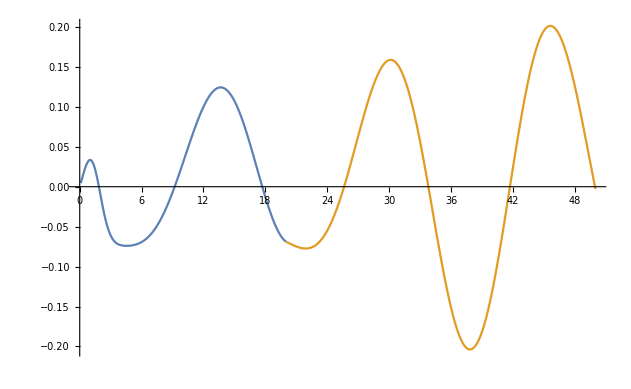

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constres0[i_]:=evecsres[[i,-len-1]]/waveres0[evalsres[[i]],rmax];
constres2[i_]:=evecsres[[i,-1]]/waveres2[evalsres[[i]],rmax];
rmaxx=50.;
constres[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[Part[evecsres⟦i⟧,1;;len]+Part[evecsres⟦i⟧,len+1;;2 len],constres0[i] waveres0[evalsres[[i]],Range[rmax+dr,rmaxx,dr]]+constres2[i] waveres2[evalsres[[i]],Range[rmax+dr,rmaxx,dr]]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
ListLinePlot[{Transpose[{rlist,constres[1] Re[Part[evecsres⟦1⟧,1;;len]+Part[evecsres⟦1⟧,len+1;;2 len]]}],Transpose[{Range[rmax,rmaxx,dr],constres[1] Re[constres0[1] waveres0[evalsres[[1]],Range[rmax,rmaxx,dr]]+constres2[1] waveres2[evalsres[[1]],Range[rmax,rmaxx,dr]]]}]},PlotRange->All]
```

```mathematica
evalsres
```

{5.97427-0.693016 ⅈ}

```mathematica
(*ListLinePlot[Transpose[{rlist,Abs[Part[evecs⟦1⟧,1;;len]]}],PlotRange->All]*)
```

```mathematica
(*ListLinePlot[Transpose[{rlist,Abs[Part[evecs⟦1⟧,len+1;;2 len]]}],PlotRange->All]*)
```

```mathematica
(*ListLinePlot[Transpose[{rlist,Abs[Part[evecs⟦1⟧,1;;len]+Part[evecs⟦1⟧,len+1;;2 len]]}],PlotRange->All]*)
```

## SCATTERING SOLUTIONS

```mathematica
(*SCATTERING SOLUTION*)
ks0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
ks2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
wavescat0[En_,r_,δ_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[0,ks0[En] r]-Sin[δ] SphericalBesselY[0,ks0[En] r]);
wavescat2[En_,r_,δ_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[2,ks2[En] r]-Sin[δ] SphericalBesselY[2,ks2[En] r]);
(*Bscat[En_?NumericQ,δ_?NumericQ,l_]:=k[En] rmax(((Cos[δ] ∂_x SphericalBesselJ[l,x]/.x->k[En] rmax)-(Sin[δ] ∂_x SphericalBesselY[l,x]/.x->k[En] rmax))/(Cos[δ]SphericalBesselJ[l,k[En] rmax]-Sin[δ]SphericalBesselY[l,k[En] rmax]));*)
Bscat0[En_?NumericQ,δ_?NumericQ]:=rmax/wavescat0[En,rmax,δ] D[wavescat0[En,r,δ],r]/.{r->rmax};
Bscat2[En_?NumericQ,δ_?NumericQ]:=rmax/wavescat2[En,rmax,δ] D[wavescat2[En,r,δ],r]/.{r->rmax};
(*HAMILTONIAN*)
Hnewscat[En_?NumericQ,δ_?NumericQ]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat0[En,δ]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat2[En,δ]/rmax-1);H];
(*RETURNS EIGEINVALUE*)
eigenvscat[En_?NumericQ,i_,δ_?NumericQ]:=({evalscat,evecscat}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ]]],First];evalscat[[i]]);
(*FINDS ENERGY LEVEL AND PHASE*)
(*findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenvscat[{En,n,δ,l}][[1]],{δ,0.,π,0.01}]]<En,n++;];phase=Table[{eigenvscat[{En,n,δ,l}][[1]],δ},{δ,0,π,0.001}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]*)
findnd[En_?NumericQ]:=Module[{n=1},While[Max[Table[eigenvscat[En,n,x],{x,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenvscat[En,n,x]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
(*MATCHES AMPLITUDE AND PLOTS*)
constscat0[i_]:=evecscat[[i,-len-1]]/wavescat0[evalscat[[i]],rmax,δ];
constscat2[i_]:=evecscat[[i,-1]]/wavescat2[evalscat[[i]],rmax,δ];
rmaxx=50.;
constscat[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[Part[evecscat⟦i⟧,1;;len]+Part[evecscat⟦i⟧,len+1;;2 len],constscat0[i] wavescat0[evalscat[[i]],Range[rmax+dr,rmaxx,dr],δ]+constscat2[i] wavescat2[evalscat[[i]],Range[rmax+dr,rmaxx,dr],δ]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
wvplot[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{evalscat,evecscat}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ]]],First];Print[{En,evalscat[[n]],n,δ}];ListLinePlot[{Transpose[{rlist,constscat[n] Abs[Part[evecscat⟦n⟧,1;;len]+Part[evecscat⟦n⟧,len+1;;2 len]]}],Transpose[{Range[rmax,rmaxx,dr],constscat[n] Abs[constscat0[n] wavescat0[evalscat[[n]],Range[rmax,rmaxx,dr],δ]+constscat2[n] wavescat2[evalscat[[n]],Range[rmax,rmaxx,dr],δ]]}]},PlotRange->All]]
```

```mathematica
(*vals[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ]]],First];Print[{En,eval[[n]],n,δ}];]*)
```

{5.97,5.97+0. ⅈ,6,0.436317+0. ⅈ}

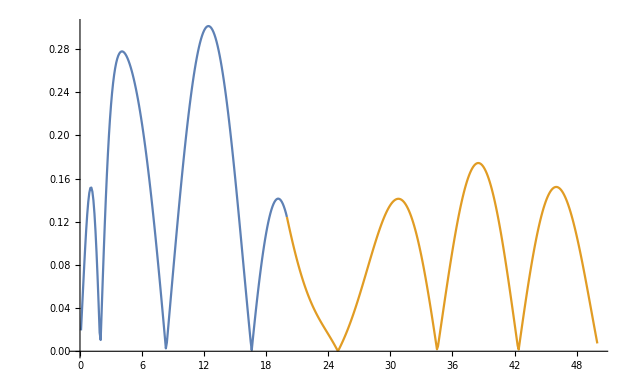
{53.02,-Graphics-}

```mathematica
wvplot[5.97]//Timing
```

```mathematica
(*ListLinePlot[{Transpose[{rlist,Part[evec[[n]],1;;len]}]},PlotRange->All]*)
```

```mathematica
(*ListLinePlot[{Transpose[{rlist,Part[evec[[n]],len+1;;2 len]}]},PlotRange->All]*)
```

```mathematica
(*ListLinePlot[{Transpose[{rlist,Part[evec[[n]],1;;len]+Part[evec[[n]],len+1;;2 len]}]},PlotRange->All]*)
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,4.5,5.5,0.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

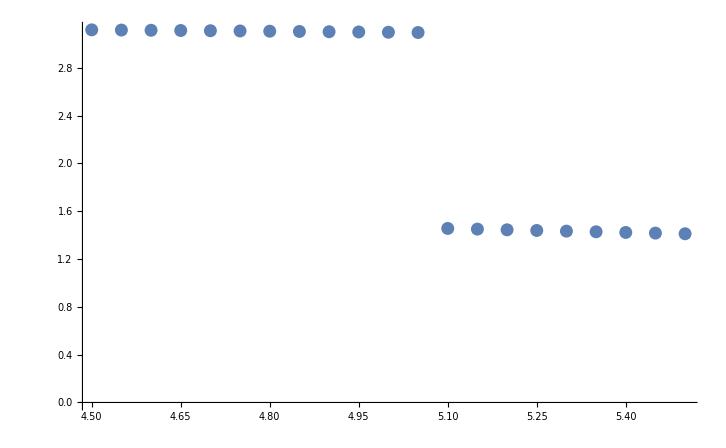

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```

```mathematica
findres[n_]:=(phase[y_?NumericQ]:=Re[FindRoot[eigenvscat[y,n,x,l]==y,{x,0.,-Pi,Pi}][[1,2]]];Subscript[δ, res]=y/.FindRoot[phase[y]==Pi/2,{y,3.2,3.,3.5}])
```

```mathematica
Subscript[δ, res]=findres[2]
```

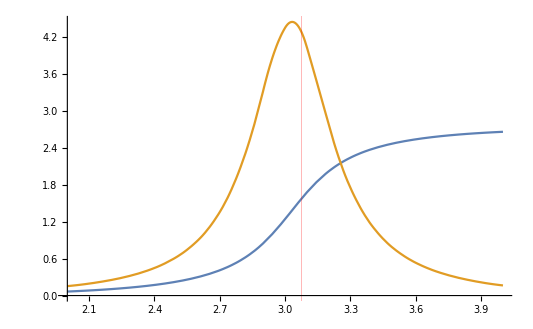

```mathematica
funcphasedata=Interpolation[phasedata,Method->"Spline"];
dfuncphasedata=funcphasedata';
Plot[Evaluate[{funcphasedata[x],dfuncphasedata[x]}],{x,2.0,4.0},GridLines->{{{Subscript[δ, res],Red}},None}]
```

```mathematica
1/(D[funcphasedata[x],x]/.x->findres[1])
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {3.5} is at the edge of the search region {3.,3.5} in coordinate 1 and the computed search direction points outside the region.

1.31784

ListLinePlot::lpn: {{{0.01,0.00488119},{0.02,0.00976453},{0.03,0.0146529},{0.04,0.0195488},{0.05,0.0244542},{0.06,0.0293708},{0.07,0.0343003},{0.08,0.039244},{0.09,0.0442032},«33»,{0.43,0.225524},{0.44,0.231227},{0.45,0.236946},{0.46,0.242682},{0.47,0.248432},{0.48,0.254197},{0.49,0.259975},{0.5,0.265767},«1950»},{}} is not a list of numbers or pairs of numbers.